# De Sitter Greens Functions (d=3)

## Setup:

```mathematica
SetDirectory["~/Documents/Causal/"];(*Directory should be set to where the causet2.wl package is saved*)
<<"causet2.wl";(*importing the package causet2.wl which has things like the sprinkling and causal/link matrices defined in it*)
```

```mathematica
m:=2
h:=1.3
n:=10000
d:=3
l:=1
"causal events" n
"~ causal relations" n^2
A=CSDeSitterDGlobalSlabFull[h,d,n];
ρ:=CSize[A] / CVolume[A]
"density" ρ
Subscript[C, 1]=SparseArray[CausalMatrix[A]];
```

10000 causal events

100000000 ~ causal relations

51.4756 density

## Whitman function (Analytical) :

```mathematica
Subscript[m, c]:=Sqrt[3]/2
M:= Sqrt[m^2+Subscript[m, c]^2]
H1=(d-1)/2+Sqrt[((d-1)/2)^2-M^2 l^2];
H2=(d-1)/2-Sqrt[((d-1)/2)^2-M^2 l^2];
norm=Gamma[H1]*Gamma[H2]/((4*π)^(d/2)*l^2*Gamma[d/2]);
W[τ_]:=norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[τ])]
Wpodal[τ_]:=norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1-Cosh[τ])]
Walpha[τ_,α_,β_]:= Cosh[2α]*W[τ]+Sinh[2α]*(Cos[β]*Re[Wpodal[τ]]-Sin[β]*Im[Wpodal[τ]])
```

## Volume Propagator

```mathematica
V=1/ρ(IdentityMatrix[n]+Subscript[C, 1]).(IdentityMatrix[n]+Subscript[C, 1]);
τSolve=Function[{vol},τ/. FindRoot[vol==2 Pi (τ/2-Tanh[τ/2]),{τ,1}]];
(*Memoize Tau so each distinct Vol is only solved once*)
Tau[vol_?NumericQ]:=Tau[vol]=Which[vol==0,0,vol>0,τSolve[vol]];
(*VolTime= Table[If[Subscript[C, 1][[i,j]]==1,Tau[V[[i,j]]],0],{i,n},{j,n}];*)
K= Table[If[Subscript[C, 1][[i,j]]==1,-2Im[W[Tau[V[[i,j]]]]],0],{i,n},{j,n}];
(*K= Table[If[Subscript[C, 1][[i,j]]==1, Cos[m Tau[V[[i,j]]]]/(2 π Tau[V[[i,j]]]),0],{i,n},{j,n}];*)
```

## Manifold Proper Time

```mathematica
MfdTime =Table[If[Subscript[C, 1][[i,j]]==1, Re[ArcCosh[1/(Cos[A[[1,i,4]]]*Cos[A[[1,j,4]]])*(A[[1,i,1]]*A[[1,j,1]]+A[[1,i,2]]*A[[1,j,2]]+A[[1,i,3]]*A[[1,j,3]]-Sin[A[[1,i,4]]]*Sin[A[[1,j,4]]])]]
,0],
{i,n},{j,n}];
(*
MfdSpace =Table[If[Subscript[C, 1][[i,j]]==1,0, Im[ArcCosh[1/(Cos[A[[1,i,4]]]*Cos[A[[1,j,4]]])*(A[[1,i,1]]*A[[1,j,1]]+A[[1,i,2]]*A[[1,j,2]]+A[[1,i,3]]*A[[1,j,3]]-Sin[A[[1,i,4]]]*Sin[A[[1,j,4]]])]]
],
{i,n},{j,n}]; *)

time=Transpose[{Flatten[MfdTime],Flatten[N[K]]}];
time=DeleteCases[Chop[time],{0,_}];
Length[time]"No. of non-zero relations"
```

19614485 No. of non-zero relations

## Whitman function for Causet :

```mathematica
iΔ=N[I*(K-Transpose[K])];
{EE,VV}=Chop[Eigensystem[iΔ]];
Q = Transpose[VV] . DiagonalMatrix[Clip[N[EE],{0, Max[N[Abs[EE]]]}]] . Conjugate[VV] // Chop;

pointsTime=Transpose[{Flatten[MfdSpace],Flatten[Re[Q]]}];
pointsTime=DeleteCases[Chop[pointsTime],{0,_}];
Length[pointsTime]"No. of non-zero relations"
(*pointsSpace=Transpose[{Flatten[MfdSpace],Flatten[Re[Q]]}];
*)
```

60905937 No. of non-zero relations

## Hadamard function (Re[W]):

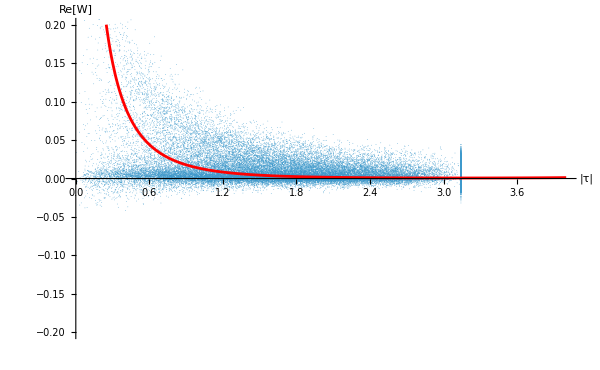

```mathematica
sample:=100000
plotLength := 4
PlottingPoints=RandomSample[pointsTime,sample];
Show[ListPlot[PlottingPoints,PlotStyle->PointSize[0.00001],ImageSize->600],Plot[Re[W[τ]],{τ,0,plotLength},PlotStyle->Red,PlotRange->{{0,plotLength},{-.2,.2}}],AxesOrigin->{0,0},PlotRange->{{0,plotLength},{-.2,.2}},AxesLabel->{Style["|τ|",16],Style["Re[W]",16]}]
(*,Plot[Re[Walpha[τ,alpha,beta]],{τ,0,8},PlotStyle->Orange,PlotRange->{{0,8},{-.1,.1}}]*)
```

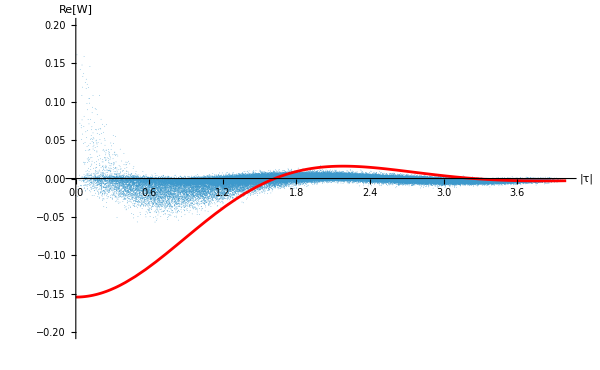

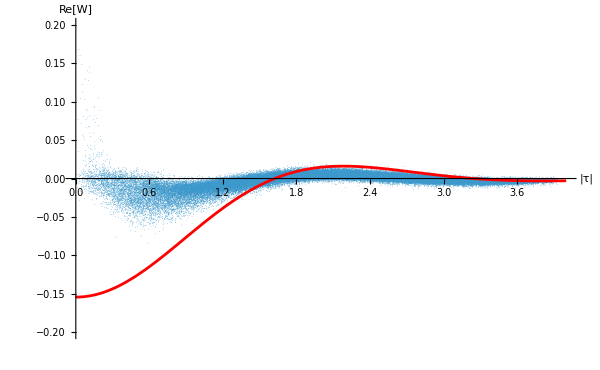
```mathematica
-Graphics-n=10000 (W)
```

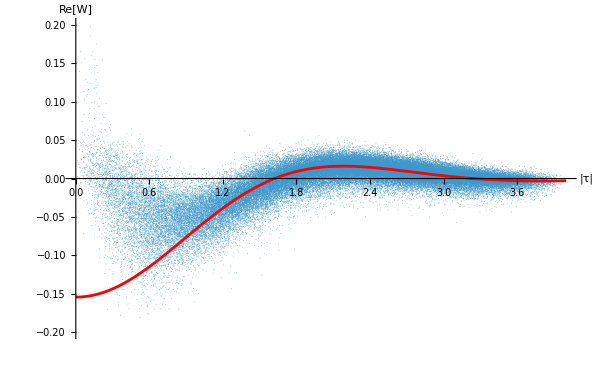
```mathematica
-Graphics-n=10000
```

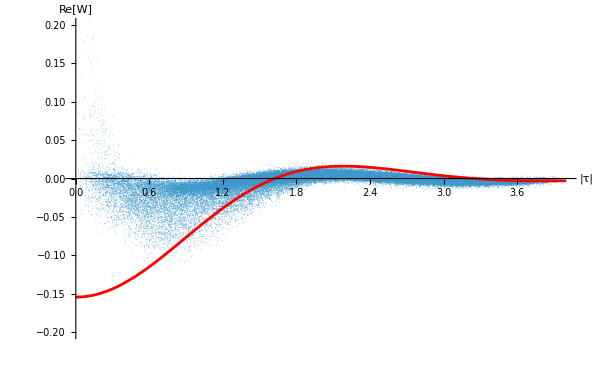
```mathematica
-Graphics-n=10000
```

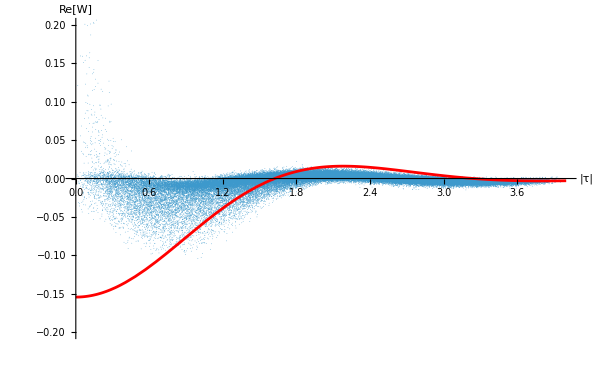
```mathematica
-Graphics-n=8000
```

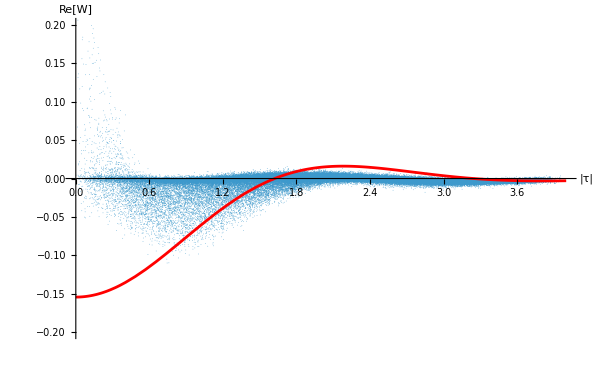
```mathematica
-Graphics-n=5000
```

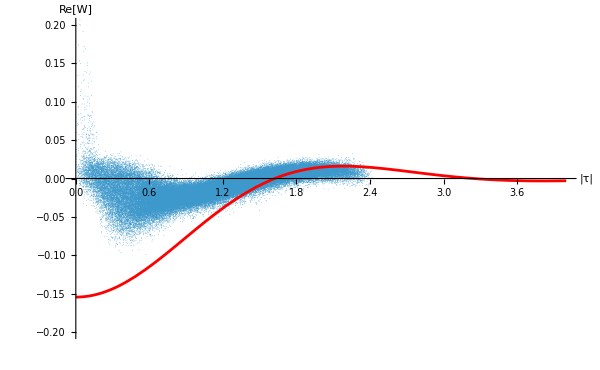

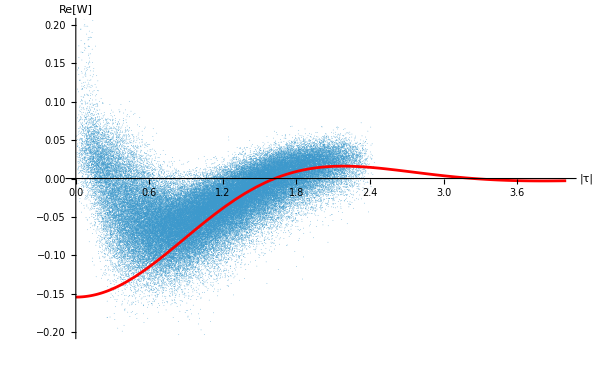

## Comparing proper times

```mathematica
TimeVol=Transpose[{Flatten[MfdTime],Flatten[N[VolTime]]}];
TimeVol=DeleteCases[Chop[TimeVol],{0,_}];
TimeLLC=Transpose[{Flatten[MfdTime],Flatten[N[LLCTime]]}];
TimeLLC=DeleteCases[Chop[TimeLLC],{0,_}];
sample:=100000
plotLength := 4
PlottingPointsVol=RandomSample[TimeVol,sample];
PlottingPointsLLC=RandomSample[TimeLLC,sample];
Show[ListPlot[PlottingPointsLLC,PlotStyle->PointSize[0.00001]],ListPlot[PlottingPointsVol,PlotStyle->{PointSize[0.00001],Orange}],Plot[τ,{τ,0,plotLength},PlotStyle->Red],PlotRange->{{0,plotLength},{-1,10}},AxesLabel->{Style["|τ|",16],Style["τ_Vol,τ_LLC",16]}]
(*ListPlot[PlottingPointsLLC,PlotStyle->PointSize[0.00001]]*)
```

-Graphics-

## Length of Longest Chain

```mathematica
L=LinkMatrix[A];
maxlength=SparseArray[Subscript[C, 1]]["NonzeroValues"];
positions=SparseArray[Subscript[C, 1]//Flatten]["NonzeroPositions"]//Flatten;
zeroCompare=Table[0,{i,1,n},{j,1,n}];
counter=1;
chains=L;

Do[
counter++;

chains=chains.L;(*finding chains of length i+1 composed of links*)

If[chains==zeroCompare,Break[]];(*if chains = 0, we can stop the loop, since no longer chains will be found*)

length=Flatten[chains][[positions]];(*flattening the matrix to a 1d array and finding only the entries corresponding to the positions of nonzero causal matrix entries*)

comparePositions=SparseArray[length//Flatten]["NonzeroPositions"]//Flatten;(*finding the positions in the new array that are nonzero*)

length=SparseArray[length]["NonzeroValues"];(*keeping only the nonzero entries of the new array*)

length=counter*HeavisideTheta[length];(*currently the length array has the number of link chains between two points, but we want the length of the chain*)
(*since the chains are longer in each iteration of the loop, we can replace the corresponding entries in the max length array with the updated values *)
maxlength[[comparePositions]]=length
(*looping up to NN-1 (i.e. L^(NN-1)), since the longest possible chain in a causet of size NN has NN-1 links*)
,{i,1,n-2}]

flattenedMaxLength=Table[0,{i,1,n*n}];(*NN^2 array of zeros*)

Do[flattenedMaxLength[[ positions[[i]] ]]=maxlength[[i]],{i,1,Length[positions]}];(*replace entries with max chain lengths according to the position of nonzero causal matrix entries in flattened causal matrix*)

MaxLength=Table[flattenedMaxLength[[1+(i-1)*n;;n+(i-1)*n]],{i,1,n}];(*unflatten to a square NN x NN matrix*)
m3=1.8701503305151406;
a=((ρ π)/12)^(1/3)m3/(2π);
KL = Table[If[Subscript[C, 1][[i,j]]==1,(a*Cos[m/(2 π a)*MaxLength[[i,j]]])/MaxLength[[i,j]],0],{i,n},{j,n}];
(*LLCTime=Table[If[Subscript[C, 1][[i,j]]==1,1/(2 π a)*MaxLength[[i,j]],0],{i,n},{j,n}];*)
```

## Fitting Alpha Vacua:

{α→-8.0164×10^-9,β→1.02336}

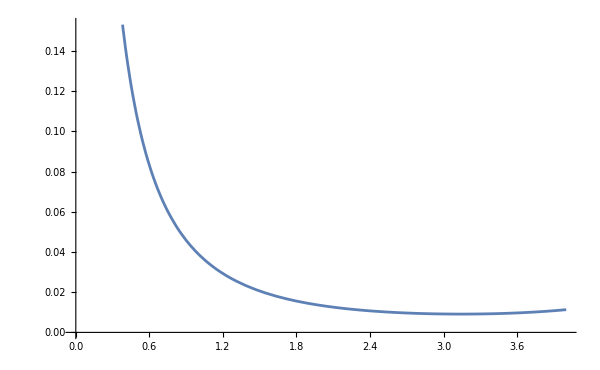

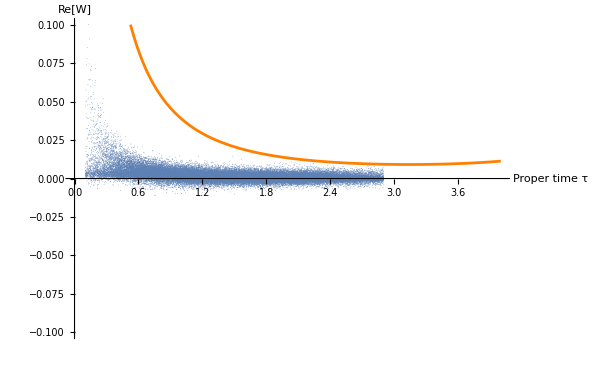

```mathematica
PlottingPoints=Select[PlottingPoints,2.9>#[[1]]>0.1&];
fit=FindFit[PlottingPoints,{Re[Cosh[2α]*W[τ]+Sinh[2α]*(Cos[β]*Re[Wpodal[τ]]-Sin[β]*Im[Wpodal[τ]])],α>=0},{{α,0},β},τ]
alpha=α/. fit;
beta=β/. fit;
Plot[Re[Walpha[τ,alpha,beta]],{τ,0,plotLength}]
Show[ListPlot[PlottingPoints,PlotStyle->PointSize[0.00001],ImageSize->600],Plot[Re[Walpha[τ,alpha,beta]],{τ,0,plotLength},PlotStyle->Orange,PlotRange->{{0,plotLength},{-.1,.1}}],AxesOrigin->{0,0},PlotRange->{{0,plotLength},{-.1,.1}},AxesLabel->{"Proper time τ","Re[W]"}]
```

## Retarded Greens Functions:

```mathematica
sample:=100000
plotLength := 4
PlottingTime=RandomSample[time,sample];
Show[ListPlot[PlottingTime,PlotStyle->PointSize[0.00001]],Plot[-2*Im[norm*Hypergeometric2F1[H1,H2,d/2,1/2*(1+Cosh[τ])]],{τ,0,plotLength},PlotStyle->Red,AspectRatio->Automatic,AxesLabel->{Style["|τ|",16],Style["Re[W]",16]},PlotRange->{{0,plotLength},{-.2,.2}}],PlotRange->{{0,plotLength},{-.2,.2}}]
```

-Graphics-

## Checking specific α/β:

```mathematica
Clear[α,β]
α:=1/2 ArcTanh[Abs[Cos[π/2 Sqrt[1-m^2]]]]
β:=0
α
β
Show[ListPlot[PlottingPoints,PlotStyle->PointSize[0.00001],ImageSize->600],Plot[Re[Walpha[τ,α,β]],{τ,0,plotLength},PlotStyle->Orange,PlotRange->{{0,plotLength},{-.1,.1}}],AxesOrigin->{0,0},PlotRange->{{0,plotLength},{-.1,.1}},AxesLabel->{"Proper time τ","Re[W]"}]
Clear[α,β]
```

∞

0

Infinity::indet: Indeterminate expression -∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-